## JPEG Compression Algorithm

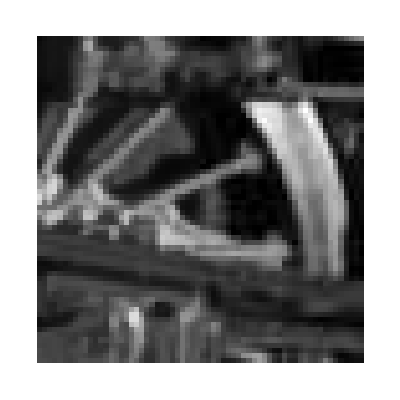
```mathematica
Manipulate[
Module[{origimg,blkdta,nblkdta,isodct,idta,qqq,qdct,qdta,redct,oldqual,oldselim,newimg},
origimg=Raster[selim];
blkdta=selBlock[selim,pt];
nblkdta=Round[blkdta 255]-128;
isodct = fDCT[nblkdta];
idta=Transpose[{Range[64],zigzag[-isodct]}];
qqq=tab[qua,quant];
qdct= Round[isodct/ qqq]  qqq;
qdta=Transpose[{Range[64],zigzag[-qdct]}];
redct=iDCT[qdct];
If[oldqual≠ qua  || oldselim≠ selim ,Table[Table[newimg=repBlock[newimg,{i,j},compressBlock[selBlock[selim,{i,j}]]];,{i,0,56,8}],{j,0,56,8}];];
oldqual=qua;
oldselim=selim;
GraphicsRow[{
GraphicsGrid[
{{
Graphics[{origimg,Red,Opacity[0.4],Rectangle[pt,pt+8]},ImageSize->{128,128},Frame->True,FrameTicks->None], 
Graphics[{Raster[newimg]},ImageSize->{128,128},Frame->True,FrameTicks->None] 
},
{
Graphics[{Raster[Table[blkdta[[i]],{i,8,1,-1}]]},ImageSize->{128,128},Frame->True,FrameTicks->None],
Graphics[{Raster[(Table[redct[[i]],{i,8,1,-1}]+128)/255.]},ImageSize->{128,128},Frame->True,FrameTicks->None]
},
{
Graphics[{Text[Style[isodct //MatrixForm,{8,Bold}]]},ImageSize->{128,128},Frame->True,FrameTicks->None],
Graphics[{Text[Style[qdct //MatrixForm,{8,Bold}]]},ImageSize->{128,128},Frame->True,FrameTicks->None]
}
},
ImageSize->{465,700},
ContentSelectable->False
],
GraphicsGrid[{{
ListPlot3D[append0[blkdta],
PlotRange->All,
BoxRatios->{1,1,0.75},
ImageSize->{200,200},
Mesh->None,
InterpolationOrder->0,
Filling->Bottom,
ColorFunction->Function[{x,y,z},GrayLevel[z]],
ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]
],
ListPlot[Flatten[-nblkdta], 
Filling->Axis,
ImageSize->{200,200},
PlotRange->All,
PlotStyle->PointSize[0.025],
PlotLabel-> "Pixel values"
]
},
{
ListPlot3D[append0[-isodct],
PlotRange->All,
BoxRatios->{1,1,0.75},
ImageSize->{200,200},
Mesh->None,
InterpolationOrder->0,
Filling->Bottom,
ColorFunction->Function[{x,y,z},GrayLevel[z]],
ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]
],
ListPlot[List /@ idta, 
Filling->Axis, 
ImageSize->{200,200},
PlotRange->All,
PlotStyle->({PointSize[0.025],If[#[[2]]==0,Red,Blue]}& /@ idta ),
PlotLabel-> "DCT - lossless"]
},
{
ListPlot3D[append0[-qdct],
PlotRange->All,
BoxRatios->{1,1,0.75},
ImageSize->{200,200},
Mesh->None,
InterpolationOrder->0,
Filling->Bottom,
ColorFunction->Function[{x,y,z},GrayLevel[z]],
ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv]
],
ListPlot[List /@ qdta, 
Filling->Axis, 
ImageSize->{200,200},
PlotRange->All,
PlotStyle->({PointSize[0.025],If[#[[2]]==0,Red,Blue]}& /@ qdta ),
PlotLabel-> "DCT - lossy"]
}},
ImageSize->{450,650},
Spacings->15,
Background->LightBlue]
},
ImageSize->{450,350},
Frame->All,
Spacings->0]],
(* Controls *)
{{qua,20,"quality"},1,99.9,ImageSize->Tiny},
{{selim,photo,"image:"},{photo->"photo",test->"test patterns"}},
{{pt,{8,24},"block:"},{0,0},{56,56},{8,8},BaselinePosition->Top,ImageSize->Tiny},
ContinuousAction->False,
ControlPlacement->Left,
TrackedSymbols->True,
SynchronousUpdating->False,
Initialization:>(
(* ISO/IEC 10918-1 FDCT and IDCT definition *)

(* Optimised for speed *)
svu=Compile[{{u,_Integer},{v,_Integer},{pix,_Real,2}},
Module[{c},
c=.25;
If[u==1,c*=0.707106781];
If[v==1,c*=0.707106781];
Round@Dot[Flatten@pix,c*Flatten@Table[Cos[0.19634954085(2x+1)(u-1)]*Cos[0.19634954085(2y+1)(v-1)],{x,0,7},{y,0,7}]]
]
];
sxy=Compile[{{x,_Integer},{y,_Integer},{coeff,_Real,2}},
Round[.25*
Dot[Flatten@coeff,
Flatten@Table[If[u>0,1.,0.707106781] If[v>0,1.,0.707106781]Cos[0.19634954085(2 (x-1) +1)(u)]Cos[0.19634954085(2 (y-1)+1)(v)],
{u,0,7},{v,0,7}]
]
]
];
fDCT[pix_]:=Table[svu[u,v,pix],{u,1,8},{v,1,8}];
iDCT[coef_]:=Table[sxy[x,y,coef],{x,8},{y,8}];




(* Standard Independent JPEG Group (Luma) Quantisation table *)
quant={
{16,11,10,16,24,40,51,61},
{12,12,14,19,26,58,60,55},
{14,13,16,24,40,57,69,56},
{14,17,22,29,51,87,80,62},
{18,22,37,56,68,109,103,77},
{24,35,55,64,81,104,113,92},
{49,64,78,87,103,121,120,101},
{72,92,95,98,112,100,103,99}
};

(* Quality dependent quantisation table construction formula *)
s[q_]:=If[q<50,5000/q,200-2 q];
tab[q_,qtab_]:=Round[(s[q] qtab +50)/100];

(* ZigZag matrix rearrange*)
zigzag[t_]:={
t[[1,1]],
t[[1,2]],t[[2,1]],
t[[3,1]],t[[2,2]],t[[1,3]],
t[[1,4]],t[[2,3]],t[[3,2]],t[[4,1]],
t[[5,1]],t[[4,2]],t[[3,3]],t[[2,4]],t[[1,5]],
t[[1,6]],t[[2,5]],t[[3,4]],t[[4,3]],t[[5,2]],t[[6,1]],
t[[7,1]],t[[6,2]],t[[5,3]],t[[4,4]],t[[3,5]],t[[2,6]],t[[1,7]],
t[[1,8]],t[[2,7]],t[[3,6]],t[[4,5]],t[[5,4]],t[[6,3]],t[[7,2]],t[[8,1]],
t[[8,2]],t[[7,3]],t[[6,4]],t[[5,5]],t[[4,6]],t[[3,7]],t[[2,8]],
t[[3,8]],t[[4,7]],t[[5,6]],t[[6,5]],t[[7,4]],t[[8,3]],
t[[8,4]],t[[7,5]],t[[6,6]],t[[5,7]],t[[4,8]],
t[[5,8]],t[[6,7]],t[[7,6]],t[[8,5]],
t[[8,6]],t[[7,7]],t[[6,8]],
t[[7,8]],t[[8,7]],
t[[8,8]]};
(* Auxiliary functions *)
(* Select the block *)
selBlock[img_,pt_]:=Table[Take[img[[j]] ,{pt[[1]]+1,pt[[1]]+8}],{j,pt[[2]]+8,pt[[2]]+1,-1}]; 
(* Append zeros to block*)
append0[blk_]:=Append[Table[Append[blk[[i]],0],{i,1,8}],{0,0,0,0,0,0,0,0,0}];
(* Compress one block *)
compressBlock[blk_]:=N[(iDCT[Round[fDCT[Round[blk 255]-128]/ qqq]  qqq]+128) /255];
(* Replace block*)
 repBlock[img_,pt_,blk_]:=
Table[If[j<pt[[2]] +1|| j>pt[[2]]+8,
img[[j]],
Table[If[i<pt[[1]]+1|| i>pt[[1]]+8,
img[[j,i]],
blk[[9-(j-pt[[2]]),i-pt[[1]]]]],
{i,1,64}]],
{j,1,64}];
(* New image table inicialisation *)
newimg=Table[Table[0,{i,1,64}],{j,1,64}];
(* 3D View inicialisation *)
vp={1.9102774676217529,-2.074271735719446,1.8703573891350447};
vv={0.,0.,1.};

(* By uncommenting next two lines and commenting the two lines with images below it's possible to import own images 64 x 64 pixels, gray levels *)
(* photo=Import[SystemDialogInput["FileOpen",NotebookDirectory[]],"GrayLevels"];
test=Import[SystemDialogInput["FileOpen",NotebookDirectory[]],"GrayLevels"]; *)
photo=Flatten[Level[-Graphics-[[1]],1],1];
test=Flatten[Level[-Graphics-[[1]],1],1];
)]
```

## CAPTION

This Demonstration shows how a two-dimensional discrete cosine transform works on the image blocks during JPEG compression and how the data is degraded by the quantization matrix. Red points in the graphs on the right side display zeros, which are important for the file size reduction. More zeros give more size reduction but worse image quality. You can choose photos and images with patterns; most of them are difficult to compress by the JPEG algorithm.

## DETAILS

The JPEG compression algorithm (which is also used in MPEG compression) is based on the two-dimensional discrete cosine transform (DCT) applied to image blocks that are 8×8 pixels in size. DCT concentrates information about the pixels in the top-left corner of the 8×8 matrix so that the importance of information in the direction of the bottom-right corner decreases. It is then possible to degrade the low information value coefficients by dividing and multiplying them by the so-called quantization matrix. These operations are rounded to whole numbers, so the smallest values become zero and can be deleted to reduce the size of the JPEG.

In the columns from the left you can see: the original image, the chosen block and DCT coefficients matrix, the compressed image, the compressed chosen block and degraded block and its coefficient matrix, a 3D representation of pixels, the DCT coefficients and degraded coefficients and chosen block output—pixels, zigzag coefficients, and zigzag degraded coefficients.

Half of the sample photo is without any compression and the other half is already compressed by the JPEG algorithm. Can you recognize which half is which by eye? Can you recognize it by the coefficients?

References

[1] Wikipedia, "JPEG." (May 2011) http://en.wikipedia.org/wiki/Jpeg.

[2] International Communication Union, "Terminal Equipment and Protocols for Telematic Services," 1993, http://www.w3.org/Graphics/JPEG/itu-t81.pdf.

[3] J. D. Kornblum, "Using JPEG Quantization Tables to Identify Imagery Processed by Software," Digital Investigation 5, 2008 S21–S25, http://dfrws.org/2008/proceedings/p21-kornblum.pdf.

THIS NOTEBOOK IS THE SOURCE CODE FROM

"JPEG Compression Algorithm" from the Wolfram Demonstrations Project
 http://demonstrations.wolfram.com/JPEGCompressionAlgorithm/

Contributed by: Jakub Serych

A full-function Wolfram Mathematica system (Version 6 or higher) is required to edit this notebook.
GET WOLFRAM MATHEMATICA »

© Wolfram Demonstrations Project & Contributors   |   Terms of Use   |   Make a new version of this Demonstration »